# 实验习题1

## 工科数学分析——数学实验

## 题1

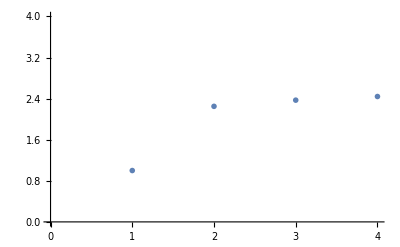

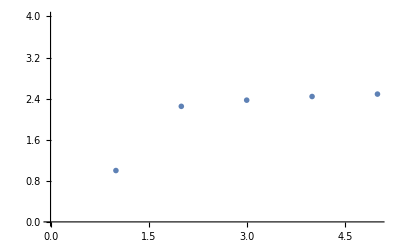

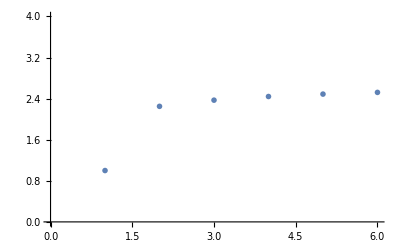

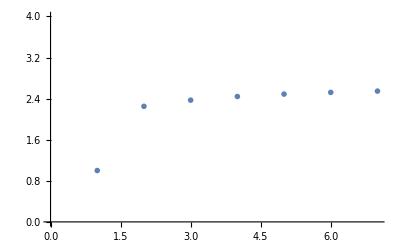

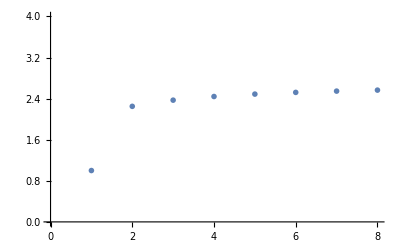

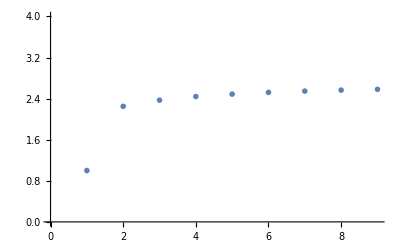

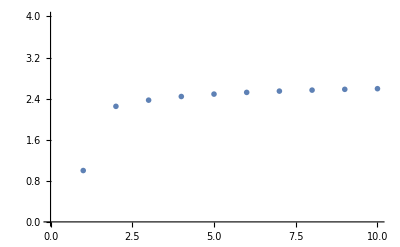

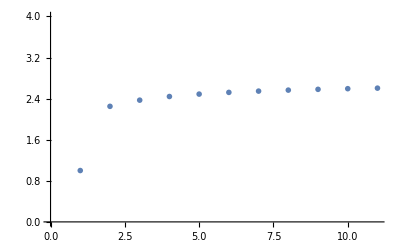

```mathematica
an={1,9/4,64/27};
Do[an=Append[an,(1/i+1)^i];
t=ListPlot[an,PlotRange->{0,4},PlotStyle->PointSize[0.01]];
Print[t],{i,4,30}
]
```

# 题2

```mathematica
f[x_]:=x^2+x;g[x_]:=1/(x+1);xn=1/2;yn=0;
For[n=2,n<=20,n++,xN=xn;yn+=g[xn];
xn=N[f[xN]];Print[N[yn,5]]

];
Print["y20=",yn]
```

0.66667

1.2381

1.67053

1.91835

1.99384

1.99996

2.

2.

2.

«10 more identical outputs»

y20=2.

可见数列{∑_(i=1)^n 1/(x_i+1)}的极限是2。